```mathematica
allinv4=Select[Tuples[{0,1},{4,4}],MatrixRank@#==4&]
```

```mathematica
delperm4=DeleteDuplicatesBy[allinv4,Sort]
```

```mathematica
delpermtrans4=DeleteDuplicatesBy[delperm4,Sort[#ᵀ]&];
```

```mathematica
indicMatrices=With[{cb=Tuples[{0,1},4]},cb.Inverse[#].(cbᵀ)/.{1->0,x_/;x!=0&&x!=1->2}&/@delpermtrans4]
```

```mathematica
deepSort[expr_]:=Map[Sort,expr,{0,-2}]
```

```mathematica
possizes[mat_]:=Module[{rows=Flatten[Position[Total/@mat,x_/;x>0]],autorows,psz},autorows=Complement[Range[Length[mat]],rows];psz=DeleteDuplicates@deepSort[Table[{Length[s],Count[Total/@(mat[[s]]ᵀ),0]}+{Length[autorows],0},{s,Subsets[rows,{1,Length[rows]}]}]];Union[psz,Reverse/@psz]]
```

```mathematica
indicMatrices[[40]]//MatrixForm
```

```mathematica
rawall4szs=possizes/@indicMatrices;
```

```mathematica
Union@@rawall4szs
```

```mathematica
all4szsfound={{5,6},{5,7},{5,8},{5,9},{5,10},{5,11},{5,12},{5,13},{5,14},{5,15},{5,16},{6,5},{6,7},{6,8},{6,9},{6,10},{6,11},{6,12},{7,5},{7,6},{7,7},{7,8},{7,9},{7,10},{8,5},{8,6},{8,7},{8,8},{8,9},{9,5},{9,6},{9,7},{9,8},{10,5},{10,6},{10,7},{11,5},{11,6},{12,5},{12,6},{13,5},{14,5},{15,5},{16,5}}
```

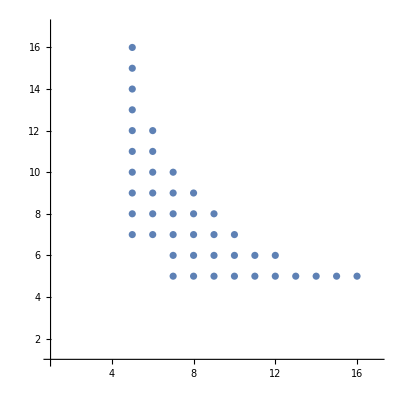

```mathematica
ListPlot[Union[%],AspectRatio->1,PlotRange->{{1,17},{1,17}}]
```

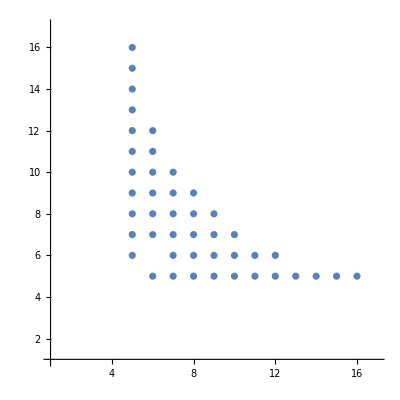

```mathematica
ListPlot[%,AspectRatio->1,PlotRange->{{1,17},{1,17}}]
```

```mathematica
{1,3,5,7}[[{1,3,4}]]
```

{1,5,7}

```mathematica
allinv5=Select[Tuples[{0,1},{5,5}],MatrixRank@#==5&]
```

$Aborted

```mathematica
d 2^d+2d/.d->4
```

72

```mathematica
some5mats=Tuples[{0,1},{5,5}];
someinv5=Select[some5mats,MatrixRank@#==5&] ;
someDelPerms5=DeleteDuplicatesBy[DeleteDuplicatesBy[someinv5,Sort],Sort[#ᵀ]&];
Length@some5mats
Length@someinv5
Length@someDelPerms5
```

33554432

12514320

14034

```mathematica
Length@someinv5
```

37580

```mathematica
someDelPerms5=DeleteDuplicatesBy[DeleteDuplicatesBy[someinv5,Sort],Sort[#ᵀ]&];
```

```mathematica
Length@someDelPerms5
```

27270

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
DumpSave["allinv5.mx",someinv5];
```

```mathematica
DumpSave["permRedinv5.mx",someDelPerms5];
```

```mathematica
MemoryInUse[]
```

11260347496

```mathematica
MemoryInUse[]
```

128891216

```mathematica
Directory[]
```

/Users/mitya/Documents/Binary-Scalar-Products-Research/Large-Family-Bounds

```mathematica
<<"permRedinv5.mx"
```

```mathematica
MemoryInUse[]
```

182059984

```mathematica
all5indic=With[{cb=Tuples[{0,1},5]},cb.Inverse[#].(cbᵀ)/.{1->0,x_/;x!=0&&x!=1->2}&/@someDelPerms5];
```

```mathematica
DumpSave["all5indic.mx",all5indic];
```

```mathematica
all5indic[[1;;100]]
```

```mathematica
{tm,all5szs}=AbsoluteTiming[Union@@(possizes/@RandomChoice[all5indic,10])];
```

$Aborted

```mathematica
all5indic[[1]]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,2,2,2,2,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,2,0,0,0,0,2,2,2,2},{0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,2},{0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,2,0,0,0,0,2,2,2,2,2,2,2,2,2,2,2,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,2,2,0,0,2,2,0,0,2,2},{0,0,0,0,0,0,0,0,0,0,2,2,0,0,2,2,0,0,0,0,0,0,0,0,0,0,2,2,0,0,2,2},{0,0,0,0,0,0,0,0,0,0,2,2,0,0,2,2,0,0,2,2,0,0,2,2,2,2,2,2,2,2,2,2},{0,0,0,0,0,0,2,2,0,0,0,0,0,0,2,2,0,0,0,0,0,0,2,2,0,0,0,0,0,0,2,2},{0,0,0,0,0,0,2,2,0,0,0,0,0,0,2,2,0,0,2,2,2,2,2,2,0,0,2,2,2,2,2,2},{0,0,0,0,0,0,2,2,0,0,2,2,2,2,2,2,0,0,0,0,0,0,2,2,0,0,2,2,2,2,2,2},{0,0,0,0,0,0,2,2,0,0,2,2,2,2,2,2,0,0,2,2,2,2,2,2,2,2,2,2,2,2,2,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2},{0,0,0,0,0,0,0,0,0,2,0,2,0,2,0,2,0,0,0,0,0,0,0,0,0,2,0,2,0,2,0,2},{0,0,0,0,0,0,0,0,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,2,2,2,2,2,2,2,2},{0,0,0,0,0,2,0,2,0,0,0,0,0,2,0,2,0,0,0,0,0,2,0,2,0,0,0,0,0,2,0,2},{0,0,0,0,0,2,0,2,0,0,0,0,0,2,0,2,0,2,0,2,2,2,2,2,0,2,0,2,2,2,2,2},{0,0,0,0,0,2,0,2,0,2,0,2,2,2,2,2,0,0,0,0,0,2,0,2,0,2,0,2,2,2,2,2},{0,0,0,0,0,2,0,2,0,2,0,2,2,2,2,2,0,2,0,2,2,2,2,2,2,2,2,2,2,2,2,2},{0,0,0,2,0,0,0,2,0,0,0,2,0,0,0,2,0,0,0,2,0,0,0,2,0,0,0,2,0,0,0,2},{0,0,0,2,0,0,0,2,0,0,0,2,0,0,0,2,0,2,2,2,0,2,2,2,0,2,2,2,0,2,2,2},{0,0,0,2,0,0,0,2,0,2,2,2,0,2,2,2,0,0,0,2,0,0,0,2,0,2,2,2,0,2,2,2},{0,0,0,2,0,0,0,2,0,2,2,2,0,2,2,2,0,2,2,2,0,2,2,2,2,2,2,2,2,2,2,2},{0,0,0,2,0,2,2,2,0,0,0,2,0,2,2,2,0,0,0,2,0,2,2,2,0,0,0,2,0,2,2,2},{0,0,0,2,0,2,2,2,0,0,0,2,0,2,2,2,0,2,2,2,2,2,2,2,0,2,2,2,2,2,2,2},{0,0,0,2,0,2,2,2,0,2,2,2,2,2,2,2,0,0,0,2,0,2,2,2,0,2,2,2,2,2,2,2},{0,0,0,2,0,2,2,2,0,2,2,2,2,2,2,2,0,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}}

```mathematica
all5indic[[1]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 2 | 2 | 0 | 0 | 0 | 0 | 2 | 2 | 2 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 2 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 2 | 2 | 0 | 0 | 0 | 0 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 2 | 2 | 0 | 0 | 2 | 2 | 0 | 0 | 2 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 2 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 2 | 2 | 0 | 0 | 2 | 2 | 0 | 0 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2
0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 2 | 2 | 2 | 2 | 2 | 2 | 0 | 0 | 2 | 2 | 2 | 2 | 2 | 2
0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 2 | 2 | 2 | 2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 2 | 2 | 2 | 2 | 2 | 2
0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 2 | 2 | 2 | 2 | 2 | 2 | 0 | 0 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 2 | 0 | 2 | 0 | 2 | 0 | 2 | 0 | 2 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 2 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 2 | 0 | 2 | 0 | 2 | 0 | 2 | 0 | 2 | 0 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2
0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 2 | 0 | 2 | 2 | 2 | 2 | 2 | 0 | 2 | 0 | 2 | 2 | 2 | 2 | 2
0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 2 | 0 | 2 | 2 | 2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 2 | 0 | 2 | 2 | 2 | 2 | 2
0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 2 | 0 | 2 | 2 | 2 | 2 | 2 | 0 | 2 | 0 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
0 | 0 | 0 | 2 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 2
0 | 0 | 0 | 2 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 2 | 0 | 2 | 2 | 2 | 0 | 2 | 2 | 2 | 0 | 2 | 2 | 2 | 0 | 2 | 2 | 2
0 | 0 | 0 | 2 | 0 | 0 | 0 | 2 | 0 | 2 | 2 | 2 | 0 | 2 | 2 | 2 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 2 | 0 | 2 | 2 | 2 | 0 | 2 | 2 | 2
0 | 0 | 0 | 2 | 0 | 0 | 0 | 2 | 0 | 2 | 2 | 2 | 0 | 2 | 2 | 2 | 0 | 2 | 2 | 2 | 0 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
0 | 0 | 0 | 2 | 0 | 2 | 2 | 2 | 0 | 0 | 0 | 2 | 0 | 2 | 2 | 2 | 0 | 0 | 0 | 2 | 0 | 2 | 2 | 2 | 0 | 0 | 0 | 2 | 0 | 2 | 2 | 2
0 | 0 | 0 | 2 | 0 | 2 | 2 | 2 | 0 | 0 | 0 | 2 | 0 | 2 | 2 | 2 | 0 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 0 | 2 | 2 | 2 | 2 | 2 | 2 | 2
0 | 0 | 0 | 2 | 0 | 2 | 2 | 2 | 0 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 0 | 0 | 0 | 2 | 0 | 2 | 2 | 2 | 0 | 2 | 2 | 2 | 2 | 2 | 2 | 2
0 | 0 | 0 | 2 | 0 | 2 | 2 | 2 | 0 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 0 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2)

```mathematica
(all5indic//Length)*2^26*26*26/(10^9*3600.)
```

176.85

```mathematica
shrinked5indic=Table[With[{r=Flatten[Position[Total/@m,x_/;x>0]],c=Flatten[Position[Total/@(mᵀ),x_/;x>0]]},m[[r,c]]/.(2->1)],{m,all5indic}];
```

```mathematica
bitcode5=Map[FromDigits[#,2]&,shrinked5indic,{2}];
```

```mathematica
bitcode5//First
```

{255,3855,491535,495615,13107,1671219,1684479,12681987,12697407,14648127,14663679,21845,2785365,2807295,21136645,21159775,24085855,24109055,38310161,38336375,41652599,41678847,63674135,63700863,67082111,67108863}

```mathematica
Export["bitcoded5.txt",StringRiffle[Table[StringRiffle[ToString/@m],{m,bitcode5}],"\n"]];
```

```mathematica
bitcode5//Length
```

14034

```mathematica
shrinked5indic[[1]]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1},{0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1},{0,0,0,0,0,0,0,1,1,1,1,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1},{0,0,0,0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1},{0,0,0,0,0,1,1,0,0,1,1,0,1,1,0,0,1,1,1,1,1,1,1,1,1,1},{0,0,1,1,0,0,0,0,0,1,1,0,0,0,0,0,1,1,0,0,0,0,0,0,1,1},{0,0,1,1,0,0,0,0,0,1,1,0,1,1,1,1,1,1,0,0,1,1,1,1,1,1},{0,0,1,1,0,1,1,1,1,1,1,0,0,0,0,0,1,1,0,0,1,1,1,1,1,1},{0,0,1,1,0,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},{0,0,0,0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1},{0,0,0,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,1,1,1,1,1,1,1,1},{0,1,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,1,0,0,0,0,0,1,0,1},{0,1,0,1,0,0,0,0,1,0,1,1,0,1,1,1,1,1,0,1,0,1,1,1,1,1},{0,1,0,1,1,0,1,1,1,1,1,0,0,0,0,1,0,1,0,1,0,1,1,1,1,1},{0,1,0,1,1,0,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,0,0,1,0,0,1,0,0,0,1,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1},{1,0,0,1,0,0,1,0,0,0,1,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1},{1,0,0,1,1,1,1,0,1,1,1,0,0,1,0,0,0,1,0,1,1,1,0,1,1,1},{1,0,0,1,1,1,1,0,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,0,0,1,0,1,1,1,0,0,1,0,1,1,1,0,0,0,1,0,1,1,1},{1,1,1,1,0,0,1,0,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,0,0,1,0,1,1,1,0,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}

```mathematica
d 2^d + 2d /. d->5
```

170

```mathematica
({26, 18, 14, 12, 11, 8, 7, 6, 5, 4, 4, 4, 3, 2}+6)*(6+Range[0,13])
```

{192,168,160,162,170,154,156,156,154,150,160,170,162,152}

```mathematica
Table[Export["bitcoded5-"<>ToString[i]<>".txt",StringRiffle[Table[StringRiffle[ToString/@m],{m,bitcode5[[(i-1)×3500+1;;i×3500]]}],"\n"]];,{i,1,3}];
```

```mathematica
Export["bitcoded5-4.txt",StringRiffle[Table[StringRiffle[ToString/@m],{m,bitcode5[[10501;;-1]]}],"\n"]];
```

```mathematica
StringCases[Import["enumeration-5-logs/results-"<>ToString[#]<>".txt"],x:NumberString:>ToExpression[x]]&/@Range[4]
```

{{26,18,14,12,11,8,7,6,5,4,4,4,3,2},{26,18,14,12,11,8,7,6,5,4,4,4,3,2},{26,18,14,12,11,8,7,6,5,4,4,4,3,2},{26,18,14,12,11,8,7,6,5,4,4,4,3,2}}

```mathematica
bitcodedIdentity=With[{m=(Tuples[{0,1},5].(Tuples[{0,1},5]ᵀ))/.{1->0,x_/;x!=0&&x!=1->2}},Map[FromDigits[#,2]&,With[{r=Flatten[Position[Total/@m,x_/;x>0]],c=Flatten[Position[Total/@(mᵀ),x_/;x>0]]},m[[r,c]]/.{2->1}],1]]
```

{38310161,21136645,12681987,63674135,2785365,1671219,41652599,491535,24085855,14648127,67082111,21845,13107,38336375,3855,21159775,12697407,63700863,255,2807295,1684479,41678847,495615,24109055,14663679,67108863}

```mathematica
Export["bitcoded5-identity.txt",StringRiffle[ToString/@bitcodedIdentity]];
```

```mathematica
StringCases[Import["enumeration-5-logs/results-identity.txt"],x:NumberString:>ToExpression[x]]
```

{26,18,14,12,11,8,7,6,5,4,4,4,3,2}

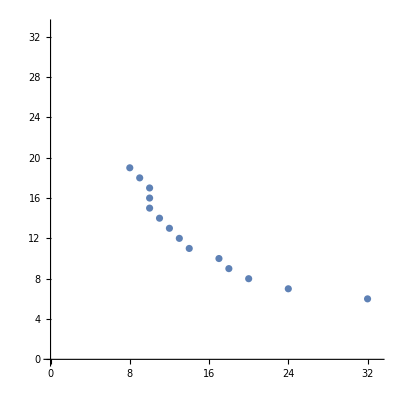

```mathematica
ListPlot[Transpose[6+{{26,18,14,12,11,8,7,6,5,4,4,4,3,2},Range[0,13]}],AspectRatio->1,PlotRange->{{0,33},{0,33}}]
```

```mathematica
maxPairs5=With[{exppairs=Transpose[6+{{26,18,14,12,11,8,7,6,5,4,4,4,3,2},Range[0,13]}]},Union[exppairs,Reverse/@exppairs]]
```

{{6,32},{7,24},{8,19},{8,20},{9,18},{10,15},{10,16},{10,17},{11,14},{12,13},{13,12},{14,11},{15,10},{16,10},{17,10},{18,9},{19,8},{20,8},{24,7},{32,6}}

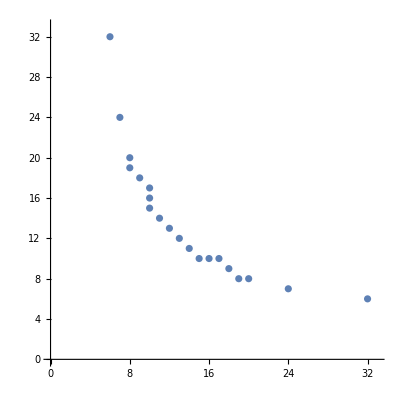

```mathematica
ListPlot[maxPairs5,AspectRatio->1,PlotRange->{{0,33},{0,33}}]
```

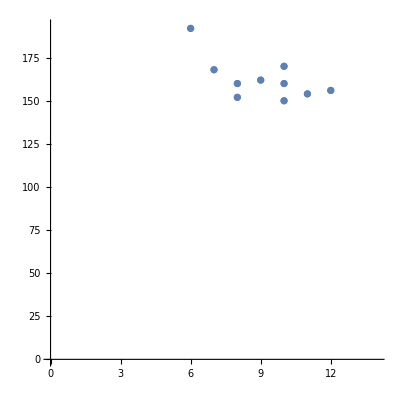

```mathematica
ListPlot[{Min[#],#[[1]]#[[2]]}&/@maxPairs5,AspectRatio->1,PlotRange->{{0,14},{0,6*32+1}}]
```

```mathematica
allPairs5=Union@@(Tuples[(x|->Range[5,x])/@#]&/@maxPairs5);
```

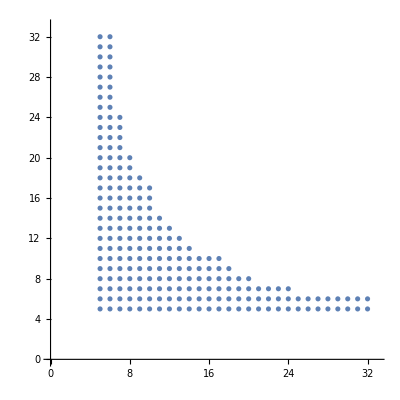

```mathematica
Show[{ListPlot[allPairs5](*,Plot[{(32*6)/x,(17*10)/x},{x,5,33},PlotStyle->Dotted]*)},AspectRatio->1,PlotRange->{{0,33},{0,33}}]
```

```mathematica
maxPairs5
```

{{6,32},{7,24},{8,19},{8,20},{9,18},{10,15},{10,16},{10,17},{11,14},{12,13},{13,12},{14,11},{15,10},{16,10},{17,10},{18,9},{19,8},{20,8},{24,7},{32,6}}

```mathematica
With[{d=5},Table[{2^(k-1)(d-k+2),(2^(d-k)+k)2^k(d-k+1)},{k,0,d}]]
```

{{7/2,192},{6,170},{10,160},{16,168},{24,192},{32,192}}

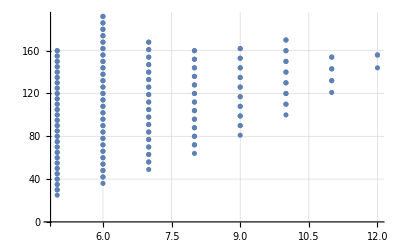

```mathematica
ListPlot[{Min[#],#[[1]]#[[2]]}&/@allPairs5,GridLines->Automatic]
```

```mathematica
allMinProd5=DeleteDuplicates[{Min[#],#[[1]]#[[2]]}&/@allPairs5];
```

```mathematica
Export["all5-min-vs-prod.dat",StringRiffle[StringRiffle[ToString/@#]&/@allMinProd5,"\n"]];
```

```mathematica
Export["all5.dat",StringRiffle[StringRiffle[ToString/@#]&/@allPairs5,"\n"]];
```